McCabe-Thiele Step-By-Step Quiz

```mathematica
(**The following initialization steps create a graphic of the X/Y axes, labels, gridlines, etc. It also gives an initial value for the RandomSeed value**)
```

```mathematica
seed=RandomInteger[{1,1000}];
```

```mathematica
base=Graphics[{
{EdgeForm[Thick],FaceForm[None],Polygon[{{0,0},{1,0},{1,1},{0,1}}]},
Table[{
(*Y axis*){Blue,Text[Style[i,17],{-.02,i-.02},{2.25,0}],Line[{{-.05,i-.02},{0,i}}]},
(*X axis*){Red,Text[Style[i,17],{i,0},{-2.25,0},{1/2,-1}],Line[{{i,0},{i+0.03/2,-0.03*√3/2}}]}},
{i,0.1,0.9,0.1}],
Rotate[Text[Style["liquid mole fraction (x_met)",17,Blue],{-.1,.98},{0,-1}],π/2,{0.05,0.7}],
Text[Style["vapor mole fraction (y_met)",17,Red],{0.8,-.15},{1,2}]
}];
```

```mathematica
gridLines=Graphics[{{Thin,GrayLevel@0.8,Table[{
(*X axis*)Line[{{i,0},{i,1}}],
(*Y Axis*)Line[{{0,i},{1,i}}],
},{i,0.05,1,0.1}]},{Thin,GrayLevel@0.5,Table[{
(*X axis*)Line[{{i,0},{i,1}}],
(*Y Axis*)Line[{{0,i},{1,i}}],
},{i,0.1,.9,0.1}]}}];
```

```mathematica
XYline=Graphics[Line[{{0,0},{1,1}}]];
```

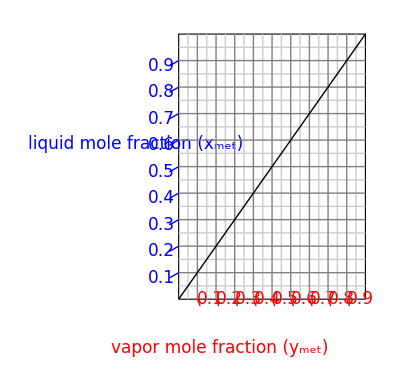

```mathematica
Show[{base,gridLines,XYline}]
```

```mathematica
SaveDefinitions->True;
```





```mathematica
Manipulate[
Module[{γ1,γ2,A12,A21,i,P,Aa,Ba,Ca,VPa,VPb,Ab,Bb,Cb,mve,tb,Rand,x2,T,y2},
(**Defines "step" as default value of 1, so program begins at "step 1"**)
Step=1;
RandomSeed[seed];
(**Equilibrium curve constants, randomized**)
A12=RandomReal[];
A21=RandomReal[{-.5,1}];
P=RandomReal[{200,1500}];
Aa=8.08097;
Ba=1582.271;
Ca=239.726;
Ab=8.07131;
Bb=1730.63;
Cb=233.426;

(**Vapor pressure of two components as a function of temperature (deg. C)**)
VPa=10^(Aa-Ba/(Ca+T));
VPb=10^(Ab-Bb/(Cb+T));

(**Murphree Efficiency is 100%**)
mve=RandomReal[{.8,1}];

(**Defines activity coefficient**)
Clear[T,i];
γ1[i_]=Exp[x2[i]^2*(A12+2*(A21-A12)*(1-x2[i]))];
γ2[i_]=Exp[(1-x2[i])^2*(A21+2*(A12-A21)*x2[i])];

(**Creates table of values defining random equilibrium curve using modified Raoult's Law**)
i=0;
While[i<101,{x2[i]=i*0.01,T[i]=FindRoot[P==VPb*γ1[i]*(1-x2[i])+VPa*γ2[i]*x2[i],{T,60},AccuracyGoal->3][[1,2]],y2[i]=x2[i]+(((VPa*γ2[i]*x2[i]/P)-x2[i])*mve)/.T->T[i],i++}];
tb=Table[{x2[i],y2[i]},{i,0,100}];

(**Plots EQ curve as a line connecting the table of values**)
eqgraphic = Graphics[Line[tb]];

(**Shows base graphics**)
Dynamic[Show[
Switch[Step,
1,{gridLines,base},
2,{gridLines,base,XYline},
3,{gridLines,base,XYline,eqgraphic}],
ImageSize->{650,420},ImagePadding->All
]]
],
(**Function to create step-by-step**)
Labeled[
Grid[{{
Column[{
Button[" new problem ",{Step=1,If[seed<1000,seed=seed+1,seed=seed-1]},ImageSize->Automatic],
Button["Show Solution",Step=Step+1,ImageSize->Automatic],
Control[{{seed,1},1,1000,1,None}]}],
PaneSelector[{
1->Item[
TextCell[
"First, the X=Y line must be drawn. This will serve as a graphical aid for the following procedure. Draw a line representing the function y=x",Medium,TextJustification->1,CellMargins->Automatic],
ItemSize->{60,11}],
2->Item[
TextCell[
"Next, the vapor-liquid equilibrium line (EQ line) must first be drawn. This defines the vapor mole fraction of the more volatile component given its liquid mole fraction. Pressure along the equilibrium curve is constant; the temperature along the equilibrium line decreases as liquid mole fraction of the more volatile component increases. The EQ line in this example was derived from Modified Raoult's Law",Medium,TextJustification->1,CellMargins->Automatic],
ItemSize->{60,11}],
3->Item[
TextCell[
"Next, the operating line of the rectifying column must be drawn. The slope of this line is a function of the reflux ratio.",Medium,TextJustification->1,CellMargins->Automatic],
ItemSize->{60,11}]},Dynamic@Step]}},
Alignment->{{Center,Center},{Center,Bottom}},Spacings->{3,0}],
Text@Style["McCabe-Thiele Step-By-Step Walkthrough and Quiz","Header","Large"],Top,Spacings->{0,2}],

SaveDefinitions->True]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation